# Evolution in a Single Population

```mathematica
Clear[pars]
```

```mathematica
pars[βs_]:=Block[{temp},temp={b1->0.2,b2->0.6,δ->0.05,κ1->10};
Join[temp,{κ2->(b1/b2)^βs κ1/.temp, β->βs},{n10->1,n20->1,tMax->500}]];
```

```mathematica
pars[1]
```

{b1→0.2,b2→0.6,δ→0.05,κ1→10,κ2→3.33333,β→1,n10→1,n20→1,tMax→500}

## Deterministic Dynamics

Differential Equations, Equilibria

```mathematica
f[i_,t_]:=n[i,t] b [i](1-(n[1,t]+n[2,t])/κ[i])(1-d)
```

```mathematica
equi=Solve[{0==f[1,t],0==f[2,t]},{n[1,t],n[2,t]}]//Simplify
```

{{n[1,t]→0,n[2,t]→κ[2]},{n[1,t]→κ[1],n[2,t]→0},{n[1,t]→0,n[2,t]→0}}

### Stability

```mathematica
jMtrx={{D[f[1,t],n[1,t]],D[f[1,t],n[2,t]]},{D[f[2,t],n[1,t]],D[f[2,t],n[2,t]]}};
```

```mathematica
Eigenvalues[jMtrx/.equi[[1]]]//FullSimplify
```

{(-1+d) b[2],-((-1+d) b[1] (κ[1]-κ[2]))/κ[1]}

```mathematica
Reduce[{(-1+d) b[2]<0,-((-1+d) b[1] (κ[1]-κ[2]))/κ[1]<0,0<d,0<b[1],0<b[2],0<κ[2],0<κ[1]},κ[2]]//FullSimplify
```

κ[1]>0&&b[2]>0&&0<d<1&&b[1]>0&&κ[2]>κ[1]

Always stable

```mathematica
Eigenvalues[jMtrx/.equi[[2]]]//FullSimplify
```

{((-1+d) b[2] (κ[1]-κ[2]))/κ[2],(-1+d) b[1]}

```mathematica
Reduce[{(-1+d) b[1]<0,((-1+d) b[2] (κ[1]-κ[2]))/κ[2]<0,0<d,0<b[1],0<b[2],0<κ[2],0<κ[1]},κ[1]]//FullSimplify
```

κ[2]>0&&b[2]>0&&0<d<1&&b[1]>0&&κ[1]>κ[2]

```mathematica
Eigenvalues[jMtrx/.equi[[3]]]//FullSimplify
```

{-(-1+d) b[1],-(-1+d) b[2]}

```mathematica
Reduce[{-(-1+d) b[1]<0,-(-1+d) b[2]<0,0<d<1,0<b[1],0<b[2],0<κ[2],0<κ[1]},κ[1]]
```

False

## Markov Chain

Markov Chain d(n)=δ

## Generator Matrix

```mathematica
e[i1_,i2_,nMax_]:=i1(nMax+1)+i2+1
```

```mathematica
Clear[tMtrx1]
tMtrx1[β_]:=tMtrx1[β]=Block[{out,i1,j1,i2,j2,r,c,nMax},nMax=Max[κ1/.pars[β],κ2/.pars[β]];out=Table[0,{j,1,(nMax+1)^2},{i,1,(nMax+1)^2}];
For[i1=0,i1≤nMax,i1++,For[i2=0,i2≤nMax,i2++,
c=e[i1,i2,nMax];
For[j1=0,j1≤nMax,j1++,For[j2=0,j2≤nMax,j2++,
r=e[j1,j2,nMax];
If[j1==i1-1&&j2==i2,out[[r,c]]+=δ i1 ];
If[j1==i1&&j2==i2-1,out[[r,c]]+=δ i2];
If[j1==i1+1&&j2==i2,out[[r,c]]+=If[i1+i2<κ1/.pars[β],b1 i1(1-(i1+i2)/κ1),0]];
If[j1==i1&&j2==i2+1,out[[r,c]]+=If[i1+i2<κ2/.pars[β],b2 i2(1-(i1+i2)/κ2),0]];
If[j1==i1&&j2==i2,out[[r,c]]+=-If[i1+i2<κ1/.pars[β],b1 i1(1-(i1+i2)/κ1),0]-If[i1+i2<κ2/.pars[β],b2 i2(1-(i1+i2)/κ2),0]-δ i1-δ i2]
]]]];
out/.pars[β]
]
```

## Master equations

```mathematica
Clear[F,ODEs,Vars,Inits]
```

Let d/dt P_(n_1,n_2)=f[n_1,n_2]

```mathematica
F[n1_,n2_,κ1_,κ2_,t_]:=-(If[n1+n2<κ1,b[1]n1 (1-(n1+n2)/κ[1]),0]+If[n1+n2<κ2,b[2]n2 (1-(n1+n2)/κ[2]),0]+δ n1+δ n2)P[n1,n2,t]+If[n1>0&&n1+n2-1<κ1,b[1](n1-1) (1-(n1+n2-1)/κ[1])P[n1-1,n2,t],0]+If[n2>0&&n1+n2-1<κ2,b[2](n2-1) (1-(n1+n2-1)/κ[2])P[n1,n2-1,t],0]+If[n1+1+n2≤ Max[κ1,κ2],δ (n1+1)P[n1+1,n2,t],0]+If[n1+n2+1≤ Max[κ1,κ2],δ(n2+1)P[n1,n2+1,t],0]
```

## Numerical Dynamics

```mathematica
ODEs[pars_]:=Flatten[Table[D[P[n1,n2,t],t]==F[n1,n2,κ1/.pars,κ2/.pars,t],{n1,0,Max[κ1,κ2]/.pars},{n2,0,(Max[κ1,κ2]/.pars)-n1}]]/.{b[1]->b1,κ[1]->κ1,κ[2]->κ2,b[2]->b1 κ1^(1/β)κ2^(-1/β)}/.pars
```

```mathematica
Vars[pars_]:=Flatten[Table[P[n1,n2,t],{n1,0,Max[κ1,κ2]/.pars},{n2,0,(Max[κ1,κ2]/.pars)-n1}]]
```

```mathematica
Inits[pars_]:=Flatten[Table[P[n1,n2,0]==If[n1==(n10/.pars)&&n2==(n20/.pars),1,0],{n1,0,Max[κ1,κ2]/.pars},{n2,0,(Max[κ1,κ2]/.pars)-n1}]]
```

```mathematica
Clear[nsol]
nsol[pars_]:=nsol[pars]=Flatten[NDSolve[Join[ODEs[pars],Inits[pars]],Vars[pars],{t,0,tMax/.pars}]]
```

```mathematica
Clear[Psol]
Psol[i_,j_,τ_,pars_]:=Psol[i,j,τ,pars]=P[i,j,t]/.nsol[pars]/.{t->τ}
```

```mathematica
SetDirectory["/Users/dehaas/Documents/densitydependence/Data"];
```

```mathematica
nMax[β_]:=Max[κ1/.pars[β],κ2/.pars[β]];
```

```mathematica
Export["test.csv", Table[{τ,Sum[i Psol[i,j,τ,pars[1]],{i,0,nMax[1]},{j,0,nMax[1]-i}],Sum[j Psol[i,j,τ,pars[1]],{i,0,nMax[1]},{j,0,nMax[1]-i}]},{τ,0,100}]]
```

test.csv

```mathematica
SystemOpen["test.csv"]
```

```mathematica
Clear[μpsol]
μpsol[τ_,pars_]:=μpsol[τ,pars]=Sum[Psol[i,j,τ,pars] i/Max[1,i+j],{i,0,Max[κ1,κ2]/.pars},{j,0,(Max[κ1,κ2]/.pars)-i}]
```

```mathematica
varpsol[τ_,pars_]:=Sum[Psol[i,j,τ,pars](i/Max[1,i+j]-μpsol[τ,pars])^2,{i,0,Max[κ1,κ2]/.pars},{j,0,(Max[κ1,κ2]/.pars)-i}]
```

```mathematica
totProb[τ_,pars_]:=Sum[Psol[i,j,τ,pars],{i,0,Max[κ1,κ2]/.pars},{j,0,(Max[κ1,κ2]/.pars)-i}]
```

```mathematica
fixProb[τ_,pars_]:=Sum[Psol[i,0,τ,pars],{i,1,Max[κ1,κ2]/.pars}]
```

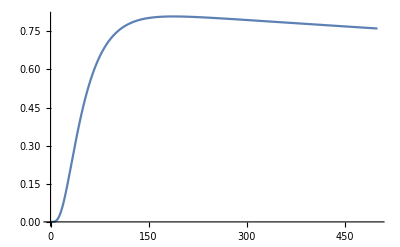

```mathematica
Plot[fixProb[τ,pars[0.5]],{τ,0,tMax/.pars[0.5]},PlotRange->All]
```

Markov Chain d(n)=δ n>1 d(1)=0

## Master equations

```mathematica
Clear[F,ODEs,Vars,Inits]
```

Let d/dt P_(n_1,n_2)=f[n_1,n_2]

```mathematica
F[n1_,n2_,κ1_,κ2_,t_]:=-(If[n1+n2<κ1,b[1]n1 (1-(n1+n2)/κ[1]),0]+If[n1+n2<κ2,b[2]n2 (1-(n1+n2)/κ[2]),0]+If[n1>1,δ n1,0]+If[n2>1,δ n2,0])P[n1,n2,t]+If[n1>0&&n1+n2-1<κ1,b[1](n1-1) (1-(n1+n2-1)/κ[1])P[n1-1,n2,t],0]+If[n2>0&&n1+n2-1<κ2,b[2](n2-1) (1-(n1+n2-1)/κ[2])P[n1,n2-1,t],0]+If[n1+1+n2≤ Max[κ1,κ2],δ (n1+1)P[n1+1,n2,t],0]+If[n1+n2+1≤ Max[κ1,κ2],δ(n2+1)P[n1,n2+1,t],0]
```

## Numerical Dynamics

```mathematica
ODEs[pars_]:=Flatten[Table[D[P[n1,n2,t],t]==F[n1,n2,κ1/.pars,κ2/.pars,t],{n1,1,(Max[κ1,κ2]/.pars)-1},{n2,1,(Max[κ1,κ2]/.pars)-n1}]]/.{b[1]->b1,κ[1]->κ1,κ[2]->κ2,b[2]->b1 κ1^(1/β)κ2^(-1/β)}/.pars
```

```mathematica
Vars[pars_]:=Flatten[Table[P[n1,n2,t],{n1,1,(Max[κ1,κ2]/.pars)-1},{n2,1,(Max[κ1,κ2]/.pars)-n1}]]
```

```mathematica
Inits[pars_]:=Flatten[Table[P[n1,n2,0]==If[n1==(n10/.pars)&&n2==(n20/.pars),1,0],{n1,1,(Max[κ1,κ2]/.pars)-1},{n2,1,(Max[κ1,κ2]/.pars)-n1}]]
```

```mathematica
Vars[pars]
```

{P[1,1,t],P[1,2,t],P[1,3,t],P[1,4,t],P[1,5,t],P[1,6,t],P[1,7,t],P[1,8,t],P[1,9,t],P[2,1,t],P[2,2,t],P[2,3,t],P[2,4,t],P[2,5,t],P[2,6,t],P[2,7,t],P[2,8,t],P[3,1,t],P[3,2,t],P[3,3,t],P[3,4,t],P[3,5,t],P[3,6,t],P[3,7,t],P[4,1,t],P[4,2,t],P[4,3,t],P[4,4,t],P[4,5,t],P[4,6,t],P[5,1,t],P[5,2,t],P[5,3,t],P[5,4,t],P[5,5,t],P[6,1,t],P[6,2,t],P[6,3,t],P[6,4,t],P[7,1,t],P[7,2,t],P[7,3,t],P[8,1,t],P[8,2,t],P[9,1,t]}

```mathematica
Clear[nsol]
nsol[pars_]:=nsol[pars]=Flatten[NDSolve[Join[ODEs[pars],Inits[pars]],Vars[pars],{t,0,tMax/.pars}]]
```

```mathematica
Clear[Psol]
Psol[i_,j_,τ_,pars_]:=Psol[i,j,τ,pars]=P[i,j,t]/.nsol[pars]/.{t->τ}
```

```mathematica
totProb[τ_,pars_]:=Sum[Psol[i,j,τ,pars],{i,1,(Max[κ1,κ2]/.pars)-1},{j,1,(Max[κ1,κ2]/.pars)-i}]
```

The probability there are x or fewer type 2s.

```mathematica
nearFixProb[τ_,pars_,x_]:=Sum[Psol[i,j,τ,pars],{j,1,x},{i,1,(Max[κ1,κ2]/.pars)-j}]
```

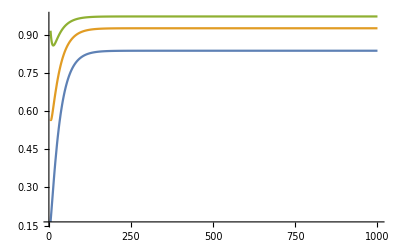

```mathematica
Plot[{nearFixProb[τ,pars,1],nearFixProb[τ,pars,2],nearFixProb[τ,pars,3]},{τ,5,1000},PlotRange->All]
```

This definition of near fixation should be okay near equilibrium because the number of type 1s should be large and hence the allele frequency near 1 if x is small.  However the early dynamics don’t make much sense.  An alternative would be to look at the probability the allele frequency exceeds a particular value over time.

The probability that the allele frequency is greater than x

```mathematica
nearFixProb2[τ_,pars_,x_]:=Sum[If[i/(i+j)>x,Psol[i,j,τ,pars],0],{i,1,(Max[κ1,κ2]/.pars)},{j,1,(Max[κ1,κ2]/.pars)-i}]
```

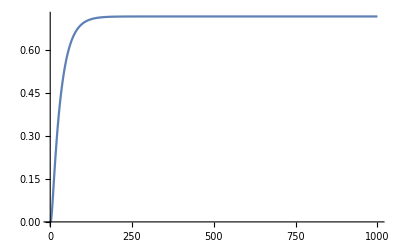

```mathematica
Plot[{nearFixProb2[τ,pars,0.8]},{τ,1,1000},PlotRange->All]
```

This should give a meaningful answer regardless of time but has some issues when carrying capacity is small which makes the set of possible allele frequency small and can make the answer highly dependent on the exact value of x chosen.

## Ensemble Moments (n_1 and n_2)

Derivation

## Substitutions and assumptions

```mathematica
first={X1[t]->μ1[t],X2[t]->μ2[t]};
second={X1[t]X2[t]->μ1[t]μ2[t]+C12[t],X1[t]^2->μ1[t]^2+V1[t],X2[t]^2->μ2[t]^2+V2[t]};
third={X1[t]^3->T1[t]+3V1[t]μ1[t]+μ1[t]^3,
X2[t]^3->T2[t]+3V2[t]μ2[t]+μ2[t]^3,
X1[t]^2 X2[t]->C112[t]+2 C12[t] μ1[t]+V1[t] μ2[t]+μ1[t]^2 μ2[t],X1[t] X2[t]^2->C122[t]+V2[t] μ1[t]+2 C12[t] μ2[t]+μ1[t] μ2[t]^2};
fourth={X1[t]^4->S1[t]+μ1[t](4 T1[t]+6 V1[t] μ1[t]+μ1[t]^3),
X1[t]^3 X2[t]->F1112[t]+3 μ1[t] (C112[t]+C12[t] μ1[t])+(T1[t]+3 V1[t] μ1[t]+μ1[t]^3) μ2[t],
X1[t]^2 X2[t]^2->F1122[t]+2 C122[t] μ1[t]+V2[t] μ1[t]^2+2 C112[t] μ2[t]+4 C12[t] μ1[t] μ2[t]+V1[t] μ2[t]^2+μ1[t]^2 μ2[t]^2,
X1[t] X2[t]^3->F1222[t]+T2[t] μ1[t]+μ2[t] (3 C122[t]+3 V2[t] μ1[t]+3 C12[t] μ2[t]+μ1[t] μ2[t]^2),
X2[t]^4->S2[t]+4 T2[t] μ2[t]+6 V2[t] μ2[t]^2
};
```

```mathematica
assump1={C112[t]->0,C122[t]->0,T1[t]->0,T2[t]->0};
```

```mathematica
assump2={S1[t]->0,S2[t]->0,F1112[t]->0,F1122[t]->0,F1222[t]->0};
```

## Means

```mathematica
dμ1dt=Collect[Expand[b[1]X1[t](1-(X1[t]+X2[t])/κ[1])(X1[t]+1-X1[t])+d X1[t](X1[t]-1-X1[t])]/.third/.second/.first,κ[1],FullSimplify]
```

(-d+b[1]) μ1[t]-(b[1] (C12[t]+V1[t]+μ1[t] (μ1[t]+μ2[t])))/κ[1]

```mathematica
dμ2dt=Collect[Expand[b[2]X2[t](1-(X1[t]+X2[t])/κ[2])(X2[t]+1-X2[t])+d X2[t](X2[t]-1-X2[t])]/.third/.second/.first,κ[2],FullSimplify]
```

(-d+b[2]) μ2[t]-(b[2] (C12[t]+V2[t]+μ2[t] (μ1[t]+μ2[t])))/κ[2]

## Variances

```mathematica
dX1X1dt=Collect[Expand[b[1]X1[t](1-(X1[t]+X2[t])/κ[1])((X1[t]+1)^2-X1[t]^2)+d X1[t]((X1[t]-1)^2-X1[t]^2)]/.third/.second/.first,κ[1],FullSimplify]
```

2 (-d+b[1]) V1[t]+μ1[t] (d+b[1]+2 (-d+b[1]) μ1[t])-(b[1] (2 C112[t]+2 T1[t]+C12[t] (1+4 μ1[t])+μ1[t] (1+2 μ1[t]) (μ1[t]+μ2[t])+V1[t] (1+6 μ1[t]+2 μ2[t])))/κ[1]

```mathematica
dX1X2dt=Collect[Expand[b[1]X1[t](1-(X1[t]+X2[t])/κ[1])((X1[t]+1)(X2[t])-X1[t]X2[t])+b[2]X2[t](1-(X1[t]+X2[t])/κ[2])((X1[t])(X2[t]+1)-X1[t]X2[t])+d X1[t]((X1[t]-1)X2[t]-X1[t]X2[t])+d X2[t]((X1[t])(X2[t]-1)-X1[t]X2[t])]/.third/.second/.first,{κ[1],κ[2]},FullSimplify]
```

(-2 d+b[1]+b[2]) (C12[t]+μ1[t] μ2[t])-(b[1] (C112[t]+C122[t]+V1[t] μ2[t]+2 C12[t] (μ1[t]+μ2[t])+μ1[t] (V2[t]+μ2[t] (μ1[t]+μ2[t]))))/κ[1]-(b[2] (C112[t]+C122[t]+V1[t] μ2[t]+2 C12[t] (μ1[t]+μ2[t])+μ1[t] (V2[t]+μ2[t] (μ1[t]+μ2[t]))))/κ[2]

```mathematica
dX2X2dt=Collect[Expand[b[2]X2[t](1-(X1[t]+X2[t])/κ[2])((X2[t]+1)^2-X2[t]^2)+d X2[t]((X2[t]-1)^2-X2[t]^2)]/.third/.second/.first,κ[2],FullSimplify]
```

2 (-d+b[2]) V2[t]+μ2[t] (d+b[2]+2 (-d+b[2]) μ2[t])-(b[2] (2 C122[t]+2 T2[t]+μ2[t] (μ1[t]+μ2[t]) (1+2 μ2[t])+C12[t] (1+4 μ2[t])+V2[t] (1+2 μ1[t]+6 μ2[t])))/κ[2]

```mathematica
dV1dt=Collect[Expand[dX1X1dt-2μ1[t]dμ1dt]/.assump1,κ[1],FullSimplify]
```

2 (-d+b[1]) V1[t]+(d+b[1]) μ1[t]-(b[1] (C12[t] (1+2 μ1[t])+μ1[t] (μ1[t]+μ2[t])+V1[t] (1+4 μ1[t]+2 μ2[t])))/κ[1]

```mathematica
dV2dt=Collect[Expand[dX2X2dt-2μ2[t]dμ2dt]/.assump1,κ[2],FullSimplify]
```

2 (-d+b[2]) V2[t]+(d+b[2]) μ2[t]-(b[2] (C12[t]+V2[t]+2 V2[t] μ1[t]+(2 C12[t]+4 V2[t]+μ1[t]) μ2[t]+μ2[t]^2))/κ[2]

```mathematica
dC12dt=Collect[Expand[dX1X2dt-μ1[t]dμ2dt-μ2[t]dμ1dt]/.assump1,{κ[2],κ[1]},FullSimplify]
```

(-2 d+b[1]+b[2]) C12[t]-(b[1] (V2[t] μ1[t]+C12[t] (2 μ1[t]+μ2[t])))/κ[1]-(b[2] (V1[t] μ2[t]+C12[t] (μ1[t]+2 μ2[t])))/κ[2]

## Skew

```mathematica
Clear[dT1dt]
```

```mathematica
dX1X1X1dt=Collect[Expand[b[1]X1[t](1-(X1[t]+X2[t])/κ[1])((X1[t]+1)^3-X1[t]^3)+d X1[t]((X1[t]-1)^3-X1[t]^3)]/.fourth/.third/.second/.first/.assump2,κ[1],FullSimplify]
```

3 (-d+b[1]) T1[t]+3 V1[t] (d+b[1]+3 (-d+b[1]) μ1[t])+μ1[t] (-d+b[1]+3 μ1[t] (d+b[1]+(-d+b[1]) μ1[t]))-1/κ[1]b[1] (3 T1[t]+V1[t]+C12[t] (1+3 μ1[t])^2+C112[t] (3+9 μ1[t])+μ1[t] (12 T1[t]+μ1[t]+3 (3 V1[t]+6 V1[t] μ1[t]+μ1[t]^2+μ1[t]^3))+(3 T1[t]+μ1[t]+3 (V1[t]+3 V1[t] μ1[t]+μ1[t]^2+μ1[t]^3)) μ2[t])

```mathematica
dX1X1X2dt=Collect[Expand[b[1]X1[t](1-(X1[t]+X2[t])/κ[1])((X1[t]+1)^2(X2[t])-X1[t]^2 X2[t])+b[2]X2[t](1-(X1[t]+X2[t])/κ[2])((X1[t])^2(X2[t]+1)-X1[t]^2 X2[t])+d X1[t]((X1[t]-1)^2 X2[t]-X1[t]^2 X2[t])]/.fourth/.third/.second/.first/.assump2,{κ[1],κ[2]},FullSimplify]
```

(-2 d+2 b[1]+b[2]) C112[t]+C12[t] (d+b[1]+2 (-2 d+2 b[1]+b[2]) μ1[t])+((-2 d+2 b[1]+b[2]) V1[t]+μ1[t] (d+b[1]+(-2 d+2 b[1]+b[2]) μ1[t])) μ2[t]+1/κ[2]b[2] (-μ1[t] (3 C112[t]+2 C122[t]+(3 C12[t]+V2[t]) μ1[t])-(2 C112[t]+T1[t]+μ1[t] (4 C12[t]+3 V1[t]+μ1[t]^2)) μ2[t]-(V1[t]+μ1[t]^2) μ2[t]^2)+1/κ[1](-b[1] (C112[t]+C122[t]+(6 C112[t]+2 C12[t]+4 C122[t]+V2[t]) μ1[t]+2 (3 C12[t]+V2[t]) μ1[t]^2)-b[1] (4 C112[t]+2 T1[t]+V1[t]+6 V1[t] μ1[t]+μ1[t]^2+2 μ1[t]^3+C12[t] (2+8 μ1[t])) μ2[t]-b[1] (2 V1[t]+μ1[t]+2 μ1[t]^2) μ2[t]^2)

```mathematica
dX1X2X2dt=Collect[Expand[b[1]X1[t](1-(X1[t]+X2[t])/κ[1])((X1[t]+1)^1(X2[t])^2-X1[t]^1 X2[t]^2)+b[2]X2[t](1-(X1[t]+X2[t])/κ[2])((X1[t])^1(X2[t]+1)^2-X1[t]^1 X2[t]^2)+d X1[t]((X1[t]-1)^1 X2[t]^2-X1[t]^1 X2[t]^2)]/.fourth/.third/.second/.first/.assump2,{κ[1],κ[2]},FullSimplify]
```

-(d-b[1]-2 b[2]) (C122[t]+V2[t] μ1[t])+b[2] μ1[t] μ2[t]+(-d+b[1]+2 b[2]) μ1[t] μ2[t]^2+C12[t] (b[2]+2 (-d+b[1]+2 b[2]) μ2[t])+1/κ[1]b[1] (-μ1[t] (2 C122[t]+T2[t]+V2[t] μ1[t])-(2 C112[t]+3 C122[t]+(4 C12[t]+3 V2[t]) μ1[t]) μ2[t]-(3 C12[t]+V1[t]+μ1[t]^2) μ2[t]^2-μ1[t] μ2[t]^3)+1/κ[2](-b[2] (C112[t]+C122[t]+(2 (C12[t]+2 C122[t]+T2[t])+V2[t]) μ1[t]+2 V2[t] μ1[t]^2)-b[2] (4 C112[t]+6 C122[t]+V1[t]+6 V2[t] μ1[t]+μ1[t]^2+C12[t] (2+8 μ1[t])) μ2[t]-b[2] (6 C12[t]+2 V1[t]+μ1[t]+2 μ1[t]^2) μ2[t]^2-2 b[2] μ1[t] μ2[t]^3)

```mathematica
dX2X2X2dt=Collect[Expand[b[2]X2[t](1-(X1[t]+X2[t])/κ[2])((X2[t]+1)^3-X2[t]^3)+d X2[t]((X2[t]-1)^3-X2[t]^3)]/.fourth/.third/.second/.first/.assump2,κ[2],FullSimplify]
```

3 (-d+b[2]) T2[t]+3 V2[t] (d+b[2]+3 (-d+b[2]) μ2[t])+μ2[t] (-d+b[2]+3 μ2[t] (d+b[2]+(-d+b[2]) μ2[t]))+1/κ[2]b[2] (-3 C122[t]-V2[t]-3 (T2[t]+(T2[t]+V2[t]) μ1[t])-C12[t] (1+3 μ2[t])^2-μ2[t] (9 C122[t]+12 T2[t]+μ1[t]+μ2[t]+9 V2[t] (1+μ1[t]+2 μ2[t])+3 μ2[t] (μ2[t]+μ1[t] (1+μ2[t]))))

{X1[t]^3→T1[t]+3V1[t]μ1[t]+μ1[t]^3,
X2[t]^3→T2[t]+3V2[t]μ2[t]+μ2[t]^3,
X1[t]^2 X2[t]→C112[t]+2 C12[t] μ1[t]+V1[t] μ2[t]+μ1[t]^2 μ2[t],X1[t]X2[t]^2→C122[t]+V2[t] μ1[t]+2 C12[t] μ2[t]+μ1[t] μ2[t]^2}

Numerical dynamics

## ODEs, Inits, and Vars

```mathematica
ODEs[pars_]:={D[μ1[t],t]== dμ1dt,D[μ2[t],t]== dμ2dt,D[V1[t],t]==dV1dt,D[C12[t],t]==dC12dt,D[V2[t],t]==dV2dt}/.{b[1]->b1,b[2]->b2,κ[1]->κ1,κ[2]->κ2,d->δ}/.pars;
Inits[pars_]:={μ1[0]==n10/.pars,μ2[0]==n20/.pars,V1[0]==0,V2[0]==0,C12[0]==0};
```

```mathematica
ODEs[pars[0.5]]
```

{μ1'[t]==0.15 μ1[t]-0.02 (C12[t]+V1[t]+μ1[t] (μ1[t]+μ2[t])),μ2'[t]==0.55 μ2[t]-0.103923 (C12[t]+V2[t]+μ2[t] (μ1[t]+μ2[t])),V1'[t]==0.3 V1[t]+0.25 μ1[t]-0.02 (C12[t] (1+2 μ1[t])+μ1[t] (μ1[t]+μ2[t])+V1[t] (1+4 μ1[t]+2 μ2[t])),C12'[t]==0.7 C12[t]-0.02 (V2[t] μ1[t]+C12[t] (2 μ1[t]+μ2[t]))-0.103923 (V1[t] μ2[t]+C12[t] (μ1[t]+2 μ2[t])),V2'[t]==1.1 V2[t]+0.65 μ2[t]-0.103923 (C12[t]+V2[t]+2 V2[t] μ1[t]+(2 C12[t]+4 V2[t]+μ1[t]) μ2[t]+μ2[t]^2)}

```mathematica
Vars={μ1[t],μ2[t],V1[t],V2[t],C12[t]};
```

```mathematica
Clear[nsol]
nsol[pars_]:=nsol[pars]=Flatten[NDSolve[Join[ODEs[pars],Inits[pars]],Vars,{t,0,tMax/.pars}]]
```

```mathematica
nsol[pars[0.5]]
```

{μ1[t]→InterpolatingFunction[{{0., 100.}}, <>][t],μ2[t]→InterpolatingFunction[{{0., 100.}}, <>][t],V1[t]→InterpolatingFunction[{{0., 100.}}, <>][t],V2[t]→InterpolatingFunction[{{0., 100.}}, <>][t],C12[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}

```mathematica
Clear[μ1sol,μ2sol,V1sol,V2sol,C12sol]
```

```mathematica
μ1sol[pars_,τ_]:=μ1sol[pars,τ]=μ1[t]/.nsol[pars]/.{t->τ}
μ2sol[pars_,τ_]:=μ2sol[pars,τ]=μ2[t]/.nsol[pars]/.{t->τ}
V1sol[pars_,τ_]:=V1sol[pars,τ]=V1[t]/.nsol[pars]/.{t->τ}
V2sol[pars_,τ_]:=V2sol[pars,τ]=V2[t]/.nsol[pars]/.{t->τ}
C12sol[pars_,τ_]:=C12sol[pars,τ]=C12[t]/.nsol[pars]/.{t->τ}
```

```mathematica
μ1sol[pars[0.5],10]
```

3.06239

```mathematica
EMPlot[pars_]:=Plot[{μ1sol[pars,τ],μ1sol[pars,τ]+Sqrt[V1sol[pars,τ]],μ1sol[pars,τ]-Sqrt[V1sol[pars,τ]],μ2sol[pars,τ],μ2sol[pars,τ]+Sqrt[V2sol[pars,τ]],μ2sol[pars,τ]-Sqrt[V2sol[pars,τ]]},{τ,0,tMax/.pars},PlotStyle->{Red,{Red,Dashed},{Red,Dashed},{Gray},{Gray,Dashed},{Gray,Dashed}}]
```

```mathematica
pars[0.3]
```

{b1→0.2,b2→0.6,δ→0.05,κ1→50,κ2→35.9612,β→0.3,n10→5,n20→5,tMax→100}

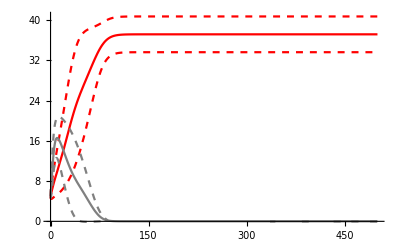

```mathematica
EMPlot[pars[0.5]]
```

```mathematica
EDynPlot[pars_]:=Plot[{μ1sol[pars,τ],μ1sol[pars,τ]+Sqrt[V1sol[pars,τ]],μ1sol[pars,τ]-Sqrt[V1sol[pars,τ]],
μ2sol[pars,τ],μ2sol[pars,τ]+Sqrt[V2sol[pars,τ]],μ2sol[pars,τ]-Sqrt[V2sol[pars,τ]]},{τ,0,tMax/.pars},PlotStyle->{Red,{Red,Dashed},{Red,Dashed},{Gray},{Gray,Dashed},{Gray,Dashed}},ImageSize->{300,150}]
```

```mathematica
90(0.5/2)^1
```

22.5

```mathematica
gridPlot[parsBase_,βa_,βb_,βc_,κa_,κb_,κc_]:=GraphicsGrid[{{EDynPlot[Join[parsBase,{κ[1]-> κa,κ[2]->κa(b[1]/b[2])^βa}/.parsBase]],EDynPlot[Join[parsBase,{κ[1]-> κa,κ[2]->κa(b[1]/b[2])^βb}/.parsBase]],EDynPlot[Join[parsBase,{κ[1]-> κa,κ[2]->κa(b[1]/b[2])^βc}/.parsBase]]},{EDynPlot[Join[parsBase,{κ[1]-> κb,κ[2]->κb(b[1]/b[2])^βa}/.parsBase]],EDynPlot[Join[parsBase,{κ[1]-> κb,κ[2]->κb(b[1]/b[2])^βb}/.parsBase]],EDynPlot[Join[parsBase,{κ[1]-> κb,κ[2]->κb(b[1]/b[2])^βc}/.parsBase]]},{EDynPlot[Join[parsBase,{κ[1]-> κc,κ[2]->κc(b[1]/b[2])^βa}/.parsBase]],EDynPlot[Join[parsBase,{κ[1]-> κc,κ[2]->κc(b[1]/b[2])^βb}/.parsBase]],EDynPlot[Join[parsBase,{κ[1]-> κc,κ[2]->κc(b[1]/b[2])^βc}/.parsBase]]}}]
```

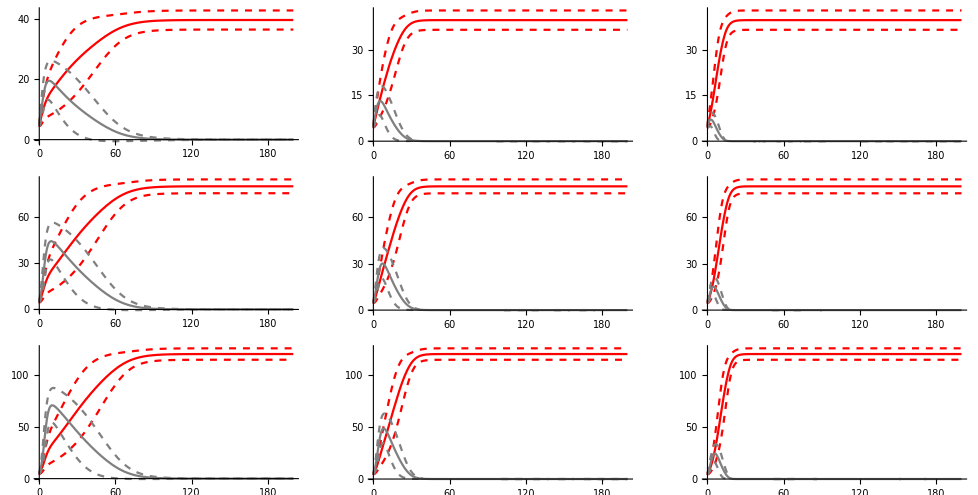

```mathematica
gridPlot[{b[1]->0.5,b[2]->0.8,X10->5,X20->5,d->0.1,tMax->200},0.5,1,2,50,100,150]
```

## Detailed balance

Individuals of type i give birth at a rate b_i (1-(n_1+n_2)/κ) while individuals of a given type die at a rate d for both types.
Once again we write down the transition probabilites using a Poisson distribution assuming the time interval Δt is short. Note that detailed balance wont work if I have two different carrying capacities but lets look at selection on birth rates only with no trade-off with carrying capacity.

## Detailed Balance

```mathematica
Clear[X1,X2]
```

```mathematica
X1[n1_,n2_,κ_]:=If[n1+n2-1≤κ,b[1](n1-1)(1-(n1+n2-1)/κ),0]/(δ n1) 
X2[n1_,n2_,κ_]:=If[n1+n2-1≤κ,b[2](n2-1)(1-(n1+n2-1)/κ),0]/(δ n2)
```

```mathematica
Clear[f]
f[n1_,n2_,κ_]:=f[n1,n2,κ]=Product[X1[c1,n2,κ],{c1,2,n1}]Product[X2[1,c2,κ],{c2,2,n2}]f1
```

```mathematica
f[n1,n2,κ]
```

f1 (Piecewise[{{-((1+n2-κ) b[1])/(2 δ κ), n1==2&&1+n2≤κ}, {((-b[1]/(δ κ))^(-1+n1) Pochhammer[n2-κ,n1])/(n1 (n2-κ)), n1>2&&n1+n2<1+κ&&1+n2<κ}, {((-b[1]/(δ κ))^Floor[-n2+κ] Pochhammer[n2-κ,1+Floor[-n2+κ]])/((n2-κ) (1+Floor[-n2+κ])), n1>2&&1+n2<κ&&n1+n2==1+κ}, {0, True}}]) (Piecewise[{{((-2+κ) b[2])/(2 δ κ), (n2==2&&κ≥2)||(n2>2&&κ==2&&n2≤κ)}, {-((-b[2]/(δ κ))^(-1+n2) Pochhammer[1-κ,n2])/(n2 (-1+κ)), n2>2&&n2<κ&&κ≥2}, {-((-b[2]/(δ κ))^(-1+Floor[κ]) Pochhammer[1-κ,Floor[κ]])/((-1+κ) Floor[κ]), n2>2&&n2==κ&&κ>2}, {0, True}}])

What is up with these 2s? Am i doing something wrong? I tried simplifying with some assumptions but it still doesn’t seem quite right.

```mathematica
Clear[totProb]
totProb[κ_]:=totProb[κ]=Sum[f[n1,n2,κ],{n1,1,κ},{n2,1,κ-n1}]
```

```mathematica
Clear[F1]
F1[κ_]:=F1[κ]=Flatten[Solve[totProb[κ]==1,f1]]
```

```mathematica
F1[κ]
```

$Aborted

```mathematica
F[n1_,n2_,κ_]:=f[n1,n2,κ]/.F1[κ]
```

```mathematica
Clear[equ]
equ[pars_]:=equ[pars]=Table[F[n1,n2,κ1/.pars],{n1,1,κ1/.pars},{n2,1,κ1/.pars}]/.{b[1]->b1,b[2]->b2,κ[1]->κ1,κ[2]->κ2}/.pars
```

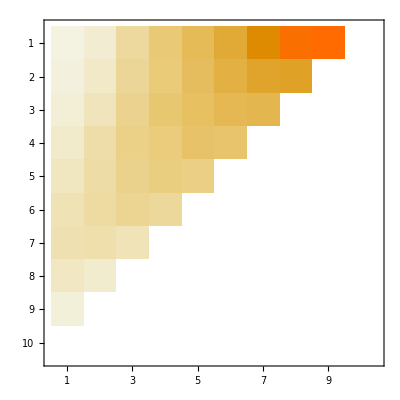

```mathematica
equ[pars]//MatrixPlot
```

# Evolution in a meta-population

## Ensemble Moments